```mathematica
(* Constants *)
k = 1.380649 * 10^-23; (*Boltzmann constant*)
H2m = 2 * 1.6605*10^-27; 
N2m = 28* 1.6605*10^-27;
O2m =  32* 1.6605*10^-27;
T0 = 73;
T1 = 273;
T2 = 473;

(* Maxwell Distribution for the absolute value of speed *)
FMaxwellDistAbs[m_, v_, T_] =
4*Pi*v^2*(m/(2*Pi*k*T))^(3/2)*Exp[-m*v^2/(2*k*T)];

(* Maxwell Distribution for the speed i-component in 3-dim space *)
FMaxwellDistSpComp[m_, vi_, T_] =
 Sqrt[m/(2*Pi*k*T)]*Exp[-m*vi^2/(2*k*T)];

(* The most probable speed *)
vP[m_, T_] = Sqrt[2*k*T / m];

(* The mean square speed *)
vMS [m_, T_] = Sqrt[3*k*T/m];
```

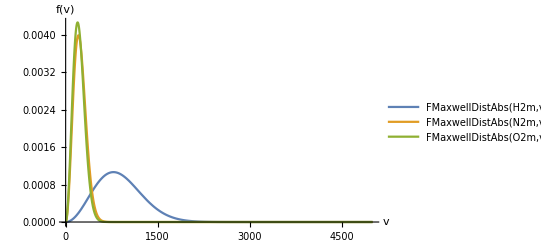

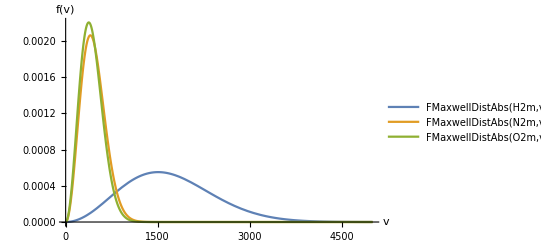

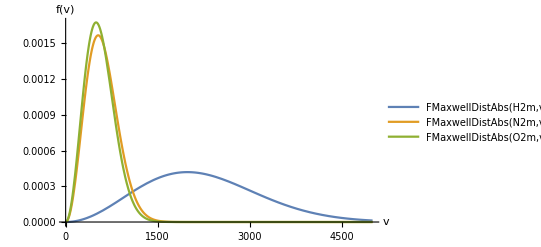

```mathematica
(* -- For the absolute value of speed -- *)
	(* T = T0 = 73K *)
Plot[
{FMaxwellDistAbs[H2m, v, T0], 
FMaxwellDistAbs[N2m, v, T0],
FMaxwellDistAbs[O2m, v, T0]},
{v, 0, 5000},
PlotLegends->"Expressions",
AxesLabel->{v, f[v]},
PlotRange->All]

	(* T = T1 = 273K *)
Plot[
{FMaxwellDistAbs[H2m, v, T1], 
FMaxwellDistAbs[N2m, v, T1],
FMaxwellDistAbs[O2m, v, T1]},
{v, 0, 5000},
PlotLegends->"Expressions",
AxesLabel->{v, f[v]},
PlotRange->All]

	(* T = T2 = 473K *)
Plot[
{FMaxwellDistAbs[H2m, v, T2], 
FMaxwellDistAbs[N2m, v, T2],
FMaxwellDistAbs[O2m, v, T2]},
{v, 0, 5000},
PlotLegends->"Expressions",
AxesLabel->{v, f[v]},
PlotRange->All]
```

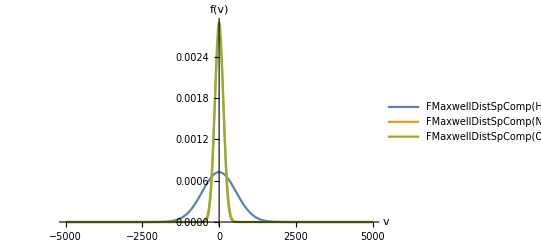

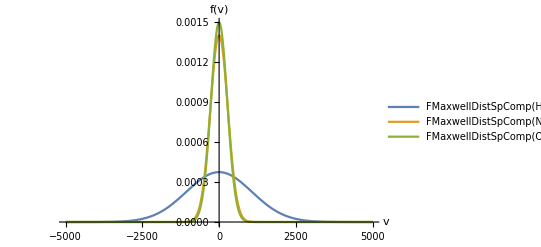

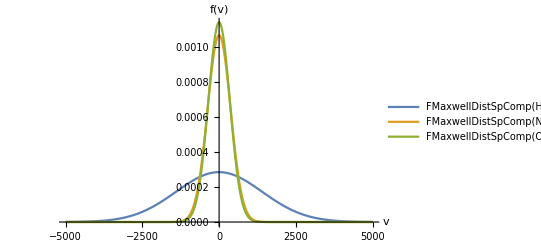

```mathematica
(* -- For the speed i-component in 3-dim space -- *)
	(* T = T0 = 73K *)
Plot[
{FMaxwellDistSpComp[H2m, v, T0], 
FMaxwellDistSpComp[N2m, v, T0],
FMaxwellDistSpComp[O2m, v, T0]},
{v, -5000, 5000},
PlotLegends->"Expressions",
AxesLabel->{v, f[v]},
PlotRange->All]

	(* T = T1 = 273K *)
Plot[
{FMaxwellDistSpComp[H2m, v, T1], 
FMaxwellDistSpComp[N2m, v, T1],
FMaxwellDistSpComp[O2m, v, T1]},
{v, -5000, 5000},
PlotLegends->"Expressions",
AxesLabel->{v, f[v]},
PlotRange->All]

	(* T = T2 = 473K *)
Plot[
{FMaxwellDistSpComp[H2m, v, T2], 
FMaxwellDistSpComp[N2m, v, T2],
FMaxwellDistSpComp[O2m, v, T2]},
{v,-5000, 5000},
PlotLegends->"Expressions",
AxesLabel->{v, f[v]},
PlotRange->All]
```

```mathematica
(* The most probable speeds *) 	
H2T0MPSpeed = vP[H2m, T0]
H2T1MPSpeed = vP[H2m, T1]
H2T2MPSpeed = vP[H2m, T2]
```

779.083

1506.62

1983.14

```mathematica
(* The mean square speeds *)
H2T0SqrSpd = vMS[H2m, T0]
H2T1SqrSpd = vMS[H2m, T1]
H2T2SqrSpd = vMS[H2m, T1]
```

954.178

1845.22

1845.22

```mathematica
(* Checking the normalization of the distribution functions *)
Integrate[FMaxwellDistSpComp[N2m, v, T0], {v, -Infinity, +Infinity}]
Integrate[FMaxwellDistAbs[N2m, v, T0], {v, 0, +Infinity}]
```

1.

1.

```mathematica
(* Calculating percentage of molecules with speeds in [0, v_avg_sqr] *)
Integrate[FMaxwellDistAbs[H2m, v, T0], {v, 0, H2T0SqrSpd}] * 100
```

60.8375

```mathematica
(* Calculating percintage of moleculas with speeds v_most_prob ± v_most_prob * 1% *)
Integrate[FMaxwellDistAbs[H2m, v, T0], {v, H2T0MPSpeed - H2T0MPSpeed * 0.01, H2T0MPSpeed + H2T0MPSpeed * 0.01}] * 100
```

1.66032

```mathematica
(* Calculating percintage of moleculas with speeds v_most_prob ± v_most_prob * 5% *)
Integrate[FMaxwellDistAbs[H2m, v, T0], {v, H2T0MPSpeed - H2T0MPSpeed * 0.01, H2T0MPSpeed + H2T0MPSpeed * 0.05}] * 100
```

4.97441